Computes  ending angular error between the z-axis of a sphere of radius ri that starts at orientation {ψ0, θ0} where angle ψ0 is  from vertical, rotated θ0 about the world z-axis, after following a circular arc with radius rc centered at [rc*cos(αc),rc*sin(αc)] with arc length ϕc
Michael Williams (Yu Huang) and Aaron T. Becker

## Things to do: given a sphere with {ri,ψ0, θ0}, what is the maximum error caused by {rc,αc,phic} as ϕc varies? Can we always pick a {rc,alphac} that is does not increase angular error? What about the ratio of Δθ_final/Δψ_final? Can we make most of the change to θ and small changes to ψ as we make the circle smaller and smaller? If so, we can take a Taylor expansion for our proof.

## Plot paths of the circle here I’d like to draw the sphere from a top down, and draw some paths and make the plane show the resulting error. This may be hard.

Try this plot!

```mathematica
ϕcMax = 2π;
Manipulate[
Module[{ri=1,αc =45Degree, ψ0=90Degree, θ0 = 225Degree,ψt,θt},
ψt =ψfinalaaron[ri,rc,αc,ϕc,ψ0,θ0];
θt =θfinal[ri,rc,αc,ϕc,ψ0,θ0];
Row[{Plot[ {ψfinal[ri,rc,αc,ϕc,ψ0,θ0],
ψfinalaaron[ri,rc,αc,ϕc,ψ0,θ0]},{ϕc,0,ϕcMax},AxesLabel->{"ϕc","ψ_final, in Degrees"},PlotLabel->"Error as a function of angle along circular path",PlotRange->{Automatic,{0,π}},PlotLegends->{"William","Aaron"},ImageSize->Medium,Epilog->{Green, PointSize[Large],Point[{ϕc,ψt}]}],
Graphics[{Gray,Rectangle[5{-1,-1},5{1,1}],
{Blue,Opacity[0.2], Disk[{0,0},ri]},
{Blue,Opacity[0.5],Disk[{rc Cos[αc],rc Sin[αc]}+{rc Cos[αc+π+ϕc],rc Sin[αc+π+ϕc]},ri]},
Black, Circle[{rc Cos[αc],rc Sin[αc]},rc],
Red, Circle[{rc Cos[αc],rc Sin[αc]},rc,(αc+π)+{0,ϕc}],
Green, PointSize[Large],Point[rc{ Cos[αc],Sin[αc]}+rc { Cos[αc+π+ϕc], Sin[αc+π+ϕc]}+ri Sin[ψt ]{Cos[θt],Sin[θt]}]
},ImageSize->Medium]}]

],{{rc,1},0.01,10},{{ϕc,ϕcMax/4},0.01,ϕcMax}]
```

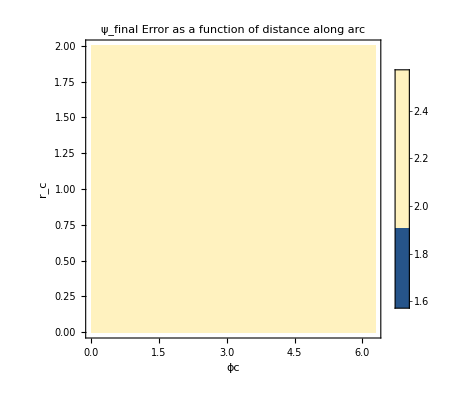

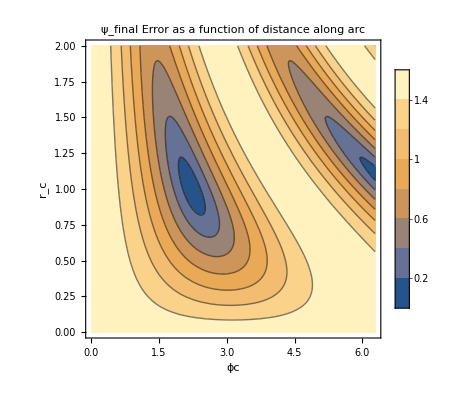

```mathematica
ψAt0 = 90Degree;
ContourPlot[ ψfinal[1,rc,45Degree,ϕc,ψAt0,225Degree],{ϕc,0,2π},{rc,0,2},FrameLabel->{"ϕc","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
ContourPlot[ ψfinalaaron[1,rc,45Degree,ϕc,ψAt0,225Degree],{ϕc,0,2π},{rc,0,2},FrameLabel->{"ϕc","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
```

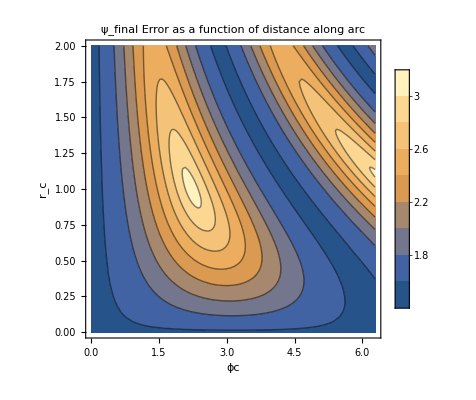

```mathematica
ContourPlot[ ψfinalaaron[1,rc,45Degree,ϕc,ψAt0,45Degree],{ϕc,0,2π},{rc,0,2},FrameLabel->{"ϕc","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
```

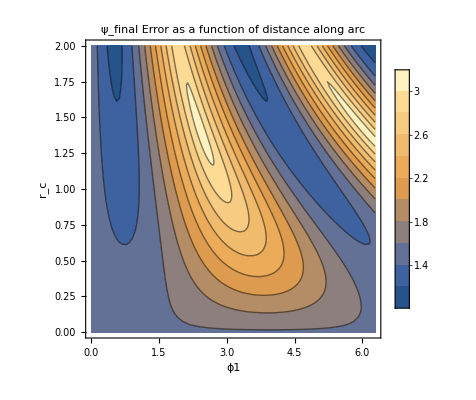

```mathematica
ContourPlot[ ψfinalaaron[1,rc,45Degree,ϕc,ψAt0,0Degree],{ϕc,0,2π},{rc,0,2},FrameLabel->{"ϕc","r_c"},PlotLabel->"ψ_final Error as a function of distance along arc",PlotLegends->Automatic]
```

```mathematica
(*Williams code -- there seems to be an error*)
ψfinal[ri_,rc_,alphac_,phic_,psi0_, theta0_]:=ArcCos[(Cos[psi0] (ri^2+rc^2 Cos[(phic √(rc^2+ri^2))/ri]))/(rc^2+ri^2)+(rc (-1+Cos[(phic √(rc^2+ri^2))/ri]) (Cos[alphac]-Sin[alphac]))/(√(rc^2+ri^2))+(rc Sin[psi0] Sin[(phic √(rc^2+ri^2))/ri] Sin[alphac-theta0])/(√(rc^2+ri^2))]
```

```mathematica
(*Aaron's calculations.  ψ is easier than θ*)
ψfinalaaron[ri_,rc_,αc_, ϕc_,ψ0_,θ0_]:=ArcCos[(Cos[ψ0] (ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕc)/ri])+rc Sin[ψ0] (-2 ri Cos[αc-θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[(√(rc^2+ri^2) ϕc)/ri]))/(rc^2+ri^2)]
θfinal[ri_,rc_,αc_, ϕc_,ψ0_,θ0_]:=ArcTan[1/(2 (rc^2+ri^2))(-2 rc √(rc^2+ri^2) Cos[ψ0] Sin[αc] Sin[(√(rc^2+ri^2) ϕc)/ri]+Cos[θ0] (rc^2+(rc^2+2 ri^2) Cos[(√(rc^2+ri^2) ϕc)/ri]) Sin[ψ0]-2 ri √(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri] Sin[ψ0]+2 rc Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2 (-2 ri Cos[αc] Cos[ψ0]+rc Cos[2 αc-θ0] Sin[ψ0])),1/(2 (rc^2+ri^2))(2 rc √(rc^2+ri^2) Cos[αc] Cos[ψ0] Sin[(√(rc^2+ri^2) ϕc)/ri]+(rc^2+(rc^2+2 ri^2) Cos[(√(rc^2+ri^2) ϕc)/ri]) Sin[θ0] Sin[ψ0]+2 ri √(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri] Sin[ψ0]+2 rc Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2 (-2 ri Cos[ψ0] Sin[αc]+rc Sin[2 αc-θ0] Sin[ψ0]))]
```

ri: the radius of the 1th ball.
rc: radius of the circle track.
alphac: I assume the ball`s initial position is on the origin of the word coordinates system and the center of the circle track is placed at (rc*cos(alphac),rc*sin(alphac))
psi0: initial psi value of the ball.
phic: specify the arc length that the ball rolled along by giving the corresponding central angle of the arc.
theta0: initial theta value of the ball.

Sphere center at {0,0,ri}
Sphere rotates about {rc Cos[αc],rc Sin[αc],0}
Vector is {rc Cos[αc],rc Sin[αc],-ri}
Then the  ball rotatess about the lollipop stick -ϕc  *rc/((ri*rc)/(√(ri^2+rc^2))) =-(√(rc^2+ri^2) ψ1)/ri

### Alternate Calculation

#### Calculate the angle the ball rotates about the lollipop stick. THe circle drawn on the sphere is of radius(ri*rc)/(√(ri^2+rc^2))

```mathematica
Clear[rc]
-ϕc*rc/((ri*rc)/(√(ri^2+rc^2))) (*lollipop rotation angle*)
```

```mathematica
-(√(rc^2+ri^2) ϕc)/ri
```

```mathematica
InitCond[ψ0_,θ0_]:=({{Sin[ψ0]Cos[θ0]}, {Sin[ψ0]Sin[θ0]}, {Cos[ψ0]}});
RotationMatrix[ϕc,{0,0,1}]//MatrixForm  (*rotation about z-axis*)
Rot1 =Simplify[Refine[RotationMatrix[-(√(rc^2+ri^2) ϕc)/ri,{rc Cos[αc],rc Sin[αc],-ri}],αc∈Reals&&ri∈Reals&&ri>0&&rc∈Reals&&rc>0]/.{Abs[Sin[αc]]->Sin[αc],Abs[Cos[αc]]->Cos[αc], Abs[Tan[αc]]-> Tan[αc]}];
```

```mathematica
({{Cos[ϕc], -Sin[ϕc], 0}, {Sin[ϕc], Cos[ϕc], 0}, {0, 0, 1}})
```

```mathematica
compositeRot=({{Cos[ϕc], -Sin[ϕc], 0}, {Sin[ϕc], Cos[ϕc], 0}, {0, 0, 1}}).Rot1.({{Sin[ψ0]Cos[θ0]}, {Sin[ψ0]Sin[θ0]}, {Cos[ψ0]}});
```

```mathematica
Simplify[ArcCos[compositeRot⟦3⟧]] (*grab 3rd element, the z-axis component, and acos[] of it*)
```

```mathematica
{ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕc)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])) Sin[ψ0])]}
```

```mathematica
FullSimplify[ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕc)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])) Sin[ψ0])]]
```

```mathematica
ArcCos[((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕc)/ri]) Cos[ψ0]+rc (-2 ri Cos[αc-θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[(√(rc^2+ri^2) ϕc)/ri]) Sin[ψ0])/(rc^2+ri^2)]
```

## The ψ angle doesn’t depend on the rotation about the z-axis

```mathematica
compEquivRot =Rot1 .({{Sin[ψ0]Cos[θ0]}, {Sin[ψ0]Sin[θ0]}, {Cos[ψ0]}});
Simplify[ArcCos[compEquivRot⟦3⟧]]
```

```mathematica
{ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕc)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])) Sin[ψ0])]}
```

```mathematica
FullSimplify[ArcCos[1/(rc^2+ri^2)((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕc)/ri]) Cos[ψ0]-rc (Sin[αc] (2 ri Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2-√(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])+Cos[αc] (2 ri Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+√(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri])) Sin[ψ0])]]
```

```mathematica
ArcCos[((ri^2+rc^2 Cos[(√(rc^2+ri^2) ϕc)/ri]) Cos[ψ0]+rc (-2 ri Cos[αc-θ0] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[(√(rc^2+ri^2) ϕc)/ri]) Sin[ψ0])/(rc^2+ri^2)]
```

```mathematica
β=-(√(rc^2+ri^2) ϕc)/ri
```

```mathematica
Simplify[ArcCos[(Cos[ψ0] (ri^2+rc^2 Cos[-β])+rc Sin[ψ0] (-2 ri Cos[αc-θ0] Sin[-β/2]^2+√(rc^2+ri^2) Sin[αc-θ0] Sin[-β]))/(rc^2+ri^2)]]
```

ArcCos[((ri^2+rc^2 Cos[β]) Cos[ψ0]-rc (2 ri Cos[αc-θ0] Sin[β/2]^2+√(rc^2+ri^2) Sin[β] Sin[αc-θ0]) Sin[ψ0])/(rc^2+ri^2)]

```mathematica
Simplify[ArcTan[compEquivRot⟦1⟧,compEquivRot⟦2⟧]]
```

```mathematica
FullSimplify[ArcTan[1/(2 (rc^2+ri^2))(-2 rc √(rc^2+ri^2) Cos[ψ0] Sin[αc] Sin[(√(rc^2+ri^2) ϕc)/ri]+(Cos[θ0] ((rc^2+2 ri^2) Cos[(√(rc^2+ri^2) ϕc)/ri]+rc^2 (1+2 Cos[2 αc] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2))-2 ri √(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri]) Sin[ψ0]+4 rc Cos[αc] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2 (-ri Cos[ψ0]+rc Sin[αc] Sin[θ0] Sin[ψ0])),1/(2 (rc^2+ri^2))(Cos[ψ0] (-4 rc ri Sin[αc] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+2 rc √(rc^2+ri^2) Cos[αc] Sin[(√(rc^2+ri^2) ϕc)/ri])+(Sin[θ0] ((rc^2+2 ri^2) Cos[(√(rc^2+ri^2) ϕc)/ri]+rc^2 (1-2 Cos[2 αc] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2))+2 Cos[θ0] (rc^2 Sin[2 αc] Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2+ri √(rc^2+ri^2) Sin[(√(rc^2+ri^2) ϕc)/ri])) Sin[ψ0])]]
```

```mathematica
ArcTan[1/(2 (rc^2+ri^2))(-2 rc √(rc^2+ri^2) Cos[ψ0] Sin[αc] Sin[(√(rc^2+ri^2) ϕc)/ri]+Cos[θ0] (rc^2+(rc^2+2 ri^2) Cos[(√(rc^2+ri^2) ϕc)/ri]) Sin[ψ0]-2 ri √(rc^2+ri^2) Sin[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri] Sin[ψ0]+2 rc Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2 (-2 ri Cos[αc] Cos[ψ0]+rc Cos[2 αc-θ0] Sin[ψ0])),1/(2 (rc^2+ri^2))(2 rc √(rc^2+ri^2) Cos[αc] Cos[ψ0] Sin[(√(rc^2+ri^2) ϕc)/ri]+(rc^2+(rc^2+2 ri^2) Cos[(√(rc^2+ri^2) ϕc)/ri]) Sin[θ0] Sin[ψ0]+2 ri √(rc^2+ri^2) Cos[θ0] Sin[(√(rc^2+ri^2) ϕc)/ri] Sin[ψ0]+2 rc Sin[(√(rc^2+ri^2) ϕc)/(2 ri)]^2 (-2 ri Cos[ψ0] Sin[αc]+rc Sin[2 αc-θ0] Sin[ψ0]))]
```

## Plot the error as a function of different variables

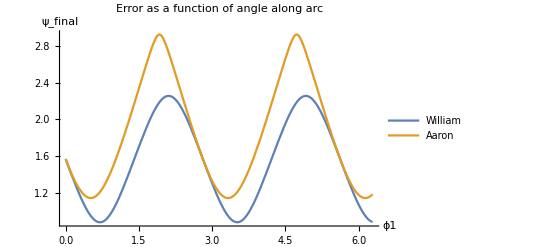

```mathematica
Plot[ {
ψfinal[1,2,45Degree,ϕc,90Degree,0],
ψfinalaaron[1,2,45Degree,ϕc,90Degree,0]},{ϕc,0,2π},AxesLabel->{"ϕc","ψ_final"},PlotLabel->"Error as a function of angle along arc",PlotLegends->{"William","Aaron"}]
```